### Start choosing the example:

```mathematica
t=20;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

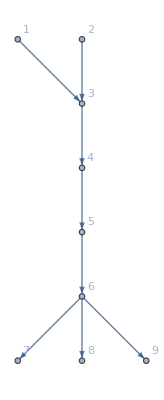
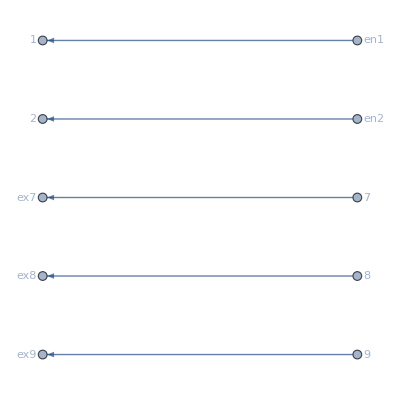
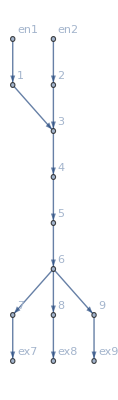
<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,200},{2,200}},Exit Vertices and Terminal Costs→{{7,0},{8,0},{9,0}},Switching Costs→{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}},VL→{1,2,3,4,5,6,7,8,9},AM→{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},EVC→{{1,200},{2,200}},EVTC→{{7,0},{8,0},{9,0}},SC→{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}},BG→-Graphics-,EntranceVertices→{1,2},InwardVertices→<|1→en1,2→en2|>,ExitVertices→{7,8,9},OutwardVertices→<|7→ex7,8→ex8,9→ex9|>,InEdges→{en1->1,en2->2},OutEdges→{7->ex7,8->ex8,9->ex9},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->3,2->3,3->4,4->5,5->6,6->7,6->8,6->9,7->ex7,8->ex8,9->ex9,en1->1,en2->2},BEL→{1->3,2->3,3->4,4->5,5->6,6->7,6->8,6->9},FVL→{1,2,3,4,5,6,7,8,9,en1,en2,ex7,ex8,ex9},jargs→{{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{7,6->7},{6,6->8},{8,6->8},{6,6->9},{9,6->9},{7,7->ex7},{ex7,7->ex7},{8,8->ex8},{ex8,8->ex8},{9,9->ex9},{ex9,9->ex9},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},uargs→{{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{7,6->7},{6,6->8},{8,6->8},{6,6->9},{9,6->9},{7,7->ex7},{ex7,7->ex7},{8,8->ex8},{ex8,8->ex8},{9,9->ex9},{ex9,9->ex9},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},AllTransitions→{{1,1->3,en1->1},{1,en1->1,1->3},{2,2->3,en2->2},{2,en2->2,2->3},{3,1->3,2->3},{3,1->3,3->4},{3,2->3,1->3},{3,2->3,3->4},{3,3->4,1->3},{3,3->4,2->3},{4,3->4,4->5},{4,4->5,3->4},{5,4->5,5->6},{5,5->6,4->5},{6,5->6,6->7},{6,5->6,6->8},{6,5->6,6->9},{6,6->7,5->6},{6,6->7,6->8},{6,6->7,6->9},{6,6->8,5->6},{6,6->8,6->7},{6,6->8,6->9},{6,6->9,5->6},{6,6->9,6->7},{6,6->9,6->8},{7,6->7,7->ex7},{7,7->ex7,6->7},{8,6->8,8->ex8},{8,8->ex8,6->8},{9,6->9,9->ex9},{9,9->ex9,6->9}},EntryArgs→{{1,en1->1},{2,en2->2}},EntryDataAssociation→<|{1,en1->1}→200,{2,en2->2}→200|>,ExitCosts→<|ex7→0,ex8→0,ex9→0|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26},jvars→<|{1,1->3}→j1,{3,1->3}→j2,{2,2->3}→j3,{3,2->3}→j4,{3,3->4}→j5,{4,3->4}→j6,{4,4->5}→j7,{5,4->5}→j8,{5,5->6}→j9,{6,5->6}→j10,{6,6->7}→j11,{7,6->7}→j12,{6,6->8}→j13,{8,6->8}→j14,{6,6->9}→j15,{9,6->9}→j16,{7,7->ex7}→j17,{ex7,7->ex7}→j18,{8,8->ex8}→j19,{ex8,8->ex8}→j20,{9,9->ex9}→j21,{ex9,9->ex9}→j22,{en1,en1->1}→j23,{1,en1->1}→j24,{en2,en2->2}→j25,{2,en2->2}→j26|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26},uvars→<|{1,1->3}→u1,{3,1->3}→u2,{2,2->3}→u3,{3,2->3}→u4,{3,3->4}→u5,{4,3->4}→u6,{4,4->5}→u7,{5,4->5}→u8,{5,5->6}→u9,{6,5->6}→u10,{6,6->7}→u11,{7,6->7}→u12,{6,6->8}→u13,{8,6->8}→u14,{6,6->9}→u15,{9,6->9}→u16,{7,7->ex7}→u17,{ex7,7->ex7}→u18,{8,8->ex8}→u19,{ex8,8->ex8}→u20,{9,9->ex9}→u21,{ex9,9->ex9}→u22,{en1,en1->1}→u23,{1,en1->1}→u24,{en2,en2->2}→u25,{2,en2->2}→u26|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32},jtvars→<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->3,en2->2}→jt3,{2,en2->2,2->3}→jt4,{3,1->3,2->3}→jt5,{3,1->3,3->4}→jt6,{3,2->3,1->3}→jt7,{3,2->3,3->4}→jt8,{3,3->4,1->3}→jt9,{3,3->4,2->3}→jt10,{4,3->4,4->5}→jt11,{4,4->5,3->4}→jt12,{5,4->5,5->6}→jt13,{5,5->6,4->5}→jt14,{6,5->6,6->7}→jt15,{6,5->6,6->8}→jt16,{6,5->6,6->9}→jt17,{6,6->7,5->6}→jt18,{6,6->7,6->8}→jt19,{6,6->7,6->9}→jt20,{6,6->8,5->6}→jt21,{6,6->8,6->7}→jt22,{6,6->8,6->9}→jt23,{6,6->9,5->6}→jt24,{6,6->9,6->7}→jt25,{6,6->9,6->8}→jt26,{7,6->7,7->ex7}→jt27,{7,7->ex7,6->7}→jt28,{8,6->8,8->ex8}→jt29,{8,8->ex8,6->8}→jt30,{9,6->9,9->ex9}→jt31,{9,9->ex9,6->9}→jt32|>,SignedCurrents→<|1->3→-j1+j2,2->3→-j3+j4,3->4→-j5+j6,4->5→-j7+j8,5->6→j10-j9,6->7→-j11+j12,6->8→-j13+j14,6->9→-j15+j16|>,SwitchingCosts→<|{1,1->3,en1->1}→1000000,{1,en1->1,1->3}→0,{2,2->3,en2->2}→1000000,{2,en2->2,2->3}→0,{3,1->3,2->3}→0,{3,1->3,3->4}→0,{3,2->3,1->3}→0,{3,2->3,3->4}→0,{3,3->4,1->3}→0,{3,3->4,2->3}→0,{4,3->4,4->5}→0,{4,4->5,3->4}→0,{5,4->5,5->6}→0,{5,5->6,4->5}→0,{6,5->6,6->7}→1,{6,5->6,6->8}→1,{6,5->6,6->9}→1,{6,6->7,5->6}→1,{6,6->7,6->8}→1,{6,6->7,6->9}→1,{6,6->8,5->6}→1,{6,6->8,6->7}→1,{6,6->8,6->9}→1,{6,6->9,5->6}→1,{6,6->9,6->7}→1,{6,6->9,6->8}→1,{7,6->7,7->ex7}→0,{7,7->ex7,6->7}→1000000,{8,6->8,8->ex8}→0,{8,8->ex8,6->8}→1000000,{9,6->9,9->ex9}→0,{9,9->ex9,6->9}→1000000|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0),EqTransitionCompCon→(jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0),NoDeadEnds→{{1,1->3},{1,en1->1},{2,2->3},{2,en2->2},{3,1->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{6,6->8},{6,6->9},{7,6->7},{7,7->ex7},{8,6->8},{8,8->ex8},{9,6->9},{9,9->ex9}},EqBalanceSplittingCurrents→j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32,BalanceSplittingCurrents→{j1-jt1,j24-jt2,j3-jt3,j26-jt4,j2-jt5-jt6,j4-jt7-jt8,j5-jt10-jt9,j6-jt11,j7-jt12,j8-jt13,j9-jt14,j10-jt15-jt16-jt17,j11-jt18-jt19-jt20,j13-jt21-jt22-jt23,j15-jt24-jt25-jt26,j12-jt27,j17-jt28,j14-jt29,j19-jt30,j16-jt31,j21-jt32},NoDeadStarts→{{3,1->3},{en1,en1->1},{3,2->3},{en2,en2->2},{1,1->3},{2,2->3},{4,3->4},{3,3->4},{5,4->5},{4,4->5},{6,5->6},{5,5->6},{7,6->7},{8,6->8},{9,6->9},{6,6->7},{ex7,7->ex7},{6,6->8},{ex8,8->ex8},{6,6->9},{ex9,9->ex9}},RuleBalanceGatheringCurrents→<|j2→jt2,j23→jt1,j4→jt4,j25→jt3,j1→jt7+jt9,j3→jt10+jt5,j6→jt6+jt8,j5→jt12,j8→jt11,j7→jt14,j10→jt13,j9→jt18+jt21+jt24,j12→jt15+jt22+jt25,j14→jt16+jt19+jt26,j16→jt17+jt20+jt23,j11→jt28,j18→jt27,j13→jt30,j20→jt29,j15→jt32,j22→jt31|>,BalanceGatheringCurrents→{-j2+jt2,-j23+jt1,-j4+jt4,-j25+jt3,-j1+jt7+jt9,-j3+jt10+jt5,-j6+jt6+jt8,-j5+jt12,-j8+jt11,-j7+jt14,-j10+jt13,-j9+jt18+jt21+jt24,-j12+jt15+jt22+jt25,-j14+jt16+jt19+jt26,-j16+jt17+jt20+jt23,-j11+jt28,-j18+jt27,-j13+jt30,-j20+jt29,-j15+jt32,-j22+jt31},EqBalanceGatheringCurrents→j2==jt2&&j23==jt1&&j4==jt4&&j25==jt3&&j1==jt7+jt9&&j3==jt10+jt5&&j6==jt6+jt8&&j5==jt12&&j8==jt11&&j7==jt14&&j10==jt13&&j9==jt18+jt21+jt24&&j12==jt15+jt22+jt25&&j14==jt16+jt19+jt26&&j16==jt17+jt20+jt23&&j11==jt28&&j18==jt27&&j13==jt30&&j20==jt29&&j15==jt32&&j22==jt31,EqEntryIn→{j24==200,j26==200},RuleEntryOut→<|j23→0,j25→0|>,RuleExitCurrentsIn→<|j17→0,j19→0,j21→0|>,RuleExitValues→<|u18→0,u20→0,u22→0|>,EqValueAuxiliaryEdges→u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22,OutRules→{{7,7->ex7,1->3}→∞,{7,7->ex7,2->3}→∞,{7,7->ex7,3->4}→∞,{7,7->ex7,4->5}→∞,{7,7->ex7,5->6}→∞,{7,7->ex7,6->7}→∞,{7,7->ex7,6->8}→∞,{7,7->ex7,6->9}→∞,{7,7->ex7,7->ex7}→∞,{7,7->ex7,8->ex8}→∞,{7,7->ex7,9->ex9}→∞,{7,7->ex7,en1->1}→∞,{7,7->ex7,en2->2}→∞,{8,8->ex8,1->3}→∞,{8,8->ex8,2->3}→∞,{8,8->ex8,3->4}→∞,{8,8->ex8,4->5}→∞,{8,8->ex8,5->6}→∞,{8,8->ex8,6->7}→∞,{8,8->ex8,6->8}→∞,{8,8->ex8,6->9}→∞,{8,8->ex8,7->ex7}→∞,{8,8->ex8,8->ex8}→∞,{8,8->ex8,9->ex9}→∞,{8,8->ex8,en1->1}→∞,{8,8->ex8,en2->2}→∞,{9,9->ex9,1->3}→∞,{9,9->ex9,2->3}→∞,{9,9->ex9,3->4}→∞,{9,9->ex9,4->5}→∞,{9,9->ex9,5->6}→∞,{9,9->ex9,6->7}→∞,{9,9->ex9,6->8}→∞,{9,9->ex9,6->9}→∞,{9,9->ex9,7->ex7}→∞,{9,9->ex9,8->ex8}→∞,{9,9->ex9,9->ex9}→∞,{9,9->ex9,en1->1}→∞,{9,9->ex9,en2->2}→∞},InRules→{{1,1->3,en1->1}→∞,{2,1->3,en2->2}→∞,{1,en1->1,en1->1}→∞,{2,en1->1,en2->2}→∞,{1,2->3,en1->1}→∞,{2,2->3,en2->2}→∞,{1,en2->2,en1->1}→∞,{2,en2->2,en2->2}→∞},EqSwitchingByVertex→{u1≤1000000+u24&&u24≤u1,u3≤1000000+u26&&u26≤u3,u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4,u6≤u7&&u7≤u6,u8≤u9&&u9≤u8,u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13,u12≤u17&&u17≤1000000+u12,u14≤u19&&u19≤1000000+u14,u16≤u21&&u21≤1000000+u16},EqCompCon→(jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0),Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16},CostArgs→<|{1,1->3}→Identity,{3,1->3}→Identity,{2,2->3}→Identity,{3,2->3}→Identity,{3,3->4}→Identity,{4,3->4}→Identity,{4,4->5}→Identity,{5,4->5}→Identity,{5,5->6}→Identity,{6,5->6}→Identity,{6,6->7}→Identity,{7,6->7}→Identity,{6,6->8}→Identity,{8,6->8}→Identity,{6,6->9}→Identity,{9,6->9}→Identity,{7,7->ex7}→Identity,{ex7,7->ex7}→(0&),{8,8->ex8}→Identity,{ex8,8->ex8}→(0&),{9,9->ex9}→Identity,{ex9,9->ex9}→(0&),{en1,en1->1}→Identity,{1,en1->1}→(0&),{en2,en2->2}→Identity,{2,en2->2}→(0&),{1,1->3,en1->1}→(10^4&),{1,en1->1,1->3}→(1/10^4&),{2,2->3,en2->2}→(10^4&),{2,en2->2,2->3}→(1/10^4&),{3,1->3,2->3}→(1/10^4&),{3,1->3,3->4}→(1/10^4&),{3,2->3,1->3}→(1/10^4&),{3,2->3,3->4}→(1/10^4&),{3,3->4,1->3}→(1/10^4&),{3,3->4,2->3}→(1/10^4&),{4,3->4,4->5}→(1/10^4&),{4,4->5,3->4}→(1/10^4&),{5,4->5,5->6}→(1/10^4&),{5,5->6,4->5}→(1/10^4&),{6,5->6,6->7}→(1/10^4&),{6,5->6,6->8}→(1/10^4&),{6,5->6,6->9}→(1/10^4&),{6,6->7,5->6}→(1/10^4&),{6,6->7,6->8}→(1/10^4&),{6,6->7,6->9}→(1/10^4&),{6,6->8,5->6}→(1/10^4&),{6,6->8,6->7}→(1/10^4&),{6,6->8,6->9}→(1/10^4&),{6,6->9,5->6}→(1/10^4&),{6,6->9,6->7}→(1/10^4&),{6,6->9,6->8}→(1/10^4&),{7,6->7,7->ex7}→(1/10^4&),{7,7->ex7,6->7}→(10^4&),{8,6->8,8->ex8}→(1/10^4&),{8,8->ex8,6->8}→(10^4&),{9,6->9,9->ex9}→(1/10^4&),{9,9->ex9,6->9}→(10^4&)|>,Nrhs→{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]},costpluscurrents→<|cpc1→-j1+j2-IntM[-j1+j2,1->3],cpc2→-j3+j4-IntM[-j3+j4,2->3],cpc3→-j5+j6-IntM[-j5+j6,3->4],cpc4→-j7+j8-IntM[-j7+j8,4->5],cpc5→j10-j9-IntM[j10-j9,5->6],cpc6→-j11+j12-IntM[-j11+j12,6->7],cpc7→-j13+j14-IntM[-j13+j14,6->8],cpc8→-j15+j16-IntM[-j15+j16,6->9]|>,EqGeneral→-j1+j2-u1+u2==cpc1&&-j3+j4-u3+u4==cpc2&&-j5+j6-u5+u6==cpc3&&-j7+j8-u7+u8==cpc4&&j10-j9+u10-u9==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u13+u14==cpc7&&-j15+j16-u15+u16==cpc8|>

-j1+j2-u1+u2==cpc1&&-j3+j4-u3+u4==cpc2&&-j5+j6-u5+u6==cpc3&&-j7+j8-u7+u8==cpc4&&j10-j9+u10-u9==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u13+u14==cpc7&&-j15+j16-u15+u16==cpc8

<|cpc1→-j1+j2-IntM[-j1+j2,1->3],cpc2→-j3+j4-IntM[-j3+j4,2->3],cpc3→-j5+j6-IntM[-j5+j6,3->4],cpc4→-j7+j8-IntM[-j7+j8,4->5],cpc5→j10-j9-IntM[j10-j9,5->6],cpc6→-j11+j12-IntM[-j11+j12,6->7],cpc7→-j13+j14-IntM[-j13+j14,6->8],cpc8→-j15+j16-IntM[-j15+j16,6->9]|>

<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→jt15,j14→jt16,j16→400-jt15-jt16,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→400-jt15-jt16,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400-jt15-jt16,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→jt15,jt28→0,jt29→jt16,jt3→0,jt30→0,jt31→400-jt15-jt16,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u12→cpc6+0-jt15+u11,u14→cpc7+0-jt16+u13,u16→cpc8+0-(400-jt15-jt16)+u15,u17→0,u19→0,u2→-200+cpc2+u25,u21→0,u24→-cpc1+cpc2+u25,u26→u25,u4→-200+cpc2+u25,u6→-600+cpc2+cpc3+u25,u8→-1000+cpc2+cpc3+cpc4+u25,u9→-1000+cpc2+cpc3+cpc4+u25,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u1→-cpc1+cpc2+u25,u10→-1400+cpc2+cpc3+cpc4+cpc5+u25,u23→-cpc1+cpc2+u25,u3→u25,u5→-200+cpc2+u25,u7→-600+cpc2+cpc3+u25|>

-j1+j2-u1+u2==cpc1&&-j3+j4-u3+u4==cpc2&&-j5+j6-u5+u6==cpc3&&-j7+j8-u7+u8==cpc4&&j10-j9+u10-u9==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u13+u14==cpc7&&-j15+j16-u15+u16==cpc8

<|cpc1→0,cpc2→0,cpc3→0,cpc4→0,cpc5→0,cpc6→0,cpc7→0,cpc8→0|>

Solve::naqs: EqCritical$20599 is not a quantified system of equations and inequalities.

critical rules?EqCritical$20599

ReplaceAll::reps: {RuleEdge} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U1},{8,U2},{9,U3}},"Switching Costs"->{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}}|>;
d2e=Data2Equations[Data/.{I1->200,I2->200,U1->0,U2->0, U3->0}]
(*MFGPreprocessing[d2e];*)
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->200,I2->200,U1->0,U2->0, U3->0}]];//AbsoluteTiming
```

```mathematica
CriticalCongestionSolver[$Failed]
```

$Failed

```mathematica
Reduce
```

```mathematica
crit
```

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,200},{2,200}},Exit Vertices and Terminal Costs→{{7,0},{8,0},{9,0}},Switching Costs→{},VL→{1,2,3,4,5,6,7,8,9},AM→{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},EVC→{{1,200},{2,200}},EVTC→{{7,0},{8,0},{9,0}},SC→{},BG→-Graphics-,EntranceVertices→{1,2},InwardVertices→<|1→en1,2→en2|>,ExitVertices→{7,8,9},OutwardVertices→<|7→ex7,8→ex8,9→ex9|>,InEdges→{en1->1,en2->2},OutEdges→{7->ex7,8->ex8,9->ex9},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->3,2->3,3->4,4->5,5->6,6->7,6->8,6->9,7->ex7,8->ex8,9->ex9,en1->1,en2->2},BEL→{1->3,2->3,3->4,4->5,5->6,6->7,6->8,6->9},FVL→{1,2,3,4,5,6,7,8,9,en1,en2,ex7,ex8,ex9},jargs→{{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{7,6->7},{6,6->8},{8,6->8},{6,6->9},{9,6->9},{7,7->ex7},{ex7,7->ex7},{8,8->ex8},{ex8,8->ex8},{9,9->ex9},{ex9,9->ex9},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},uargs→{{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{7,6->7},{6,6->8},{8,6->8},{6,6->9},{9,6->9},{7,7->ex7},{ex7,7->ex7},{8,8->ex8},{ex8,8->ex8},{9,9->ex9},{ex9,9->ex9},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},AllTransitions→{{1,1->3,en1->1},{1,en1->1,1->3},{2,2->3,en2->2},{2,en2->2,2->3},{3,1->3,2->3},{3,1->3,3->4},{3,2->3,1->3},{3,2->3,3->4},{3,3->4,1->3},{3,3->4,2->3},{4,3->4,4->5},{4,4->5,3->4},{5,4->5,5->6},{5,5->6,4->5},{6,5->6,6->7},{6,5->6,6->8},{6,5->6,6->9},{6,6->7,5->6},{6,6->7,6->8},{6,6->7,6->9},{6,6->8,5->6},{6,6->8,6->7},{6,6->8,6->9},{6,6->9,5->6},{6,6->9,6->7},{6,6->9,6->8},{7,6->7,7->ex7},{7,7->ex7,6->7},{8,6->8,8->ex8},{8,8->ex8,6->8},{9,6->9,9->ex9},{9,9->ex9,6->9}},EntryArgs→{{1,en1->1},{2,en2->2}},EntryDataAssociation→<|{1,en1->1}→200,{2,en2->2}→200|>,ExitCosts→<|ex7→0,ex8→0,ex9→0|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26},jvars→<|{1,1->3}→j1,{3,1->3}→j2,{2,2->3}→j3,{3,2->3}→j4,{3,3->4}→j5,{4,3->4}→j6,{4,4->5}→j7,{5,4->5}→j8,{5,5->6}→j9,{6,5->6}→j10,{6,6->7}→j11,{7,6->7}→j12,{6,6->8}→j13,{8,6->8}→j14,{6,6->9}→j15,{9,6->9}→j16,{7,7->ex7}→j17,{ex7,7->ex7}→j18,{8,8->ex8}→j19,{ex8,8->ex8}→j20,{9,9->ex9}→j21,{ex9,9->ex9}→j22,{en1,en1->1}→j23,{1,en1->1}→j24,{en2,en2->2}→j25,{2,en2->2}→j26|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26},uvars→<|{1,1->3}→u1,{3,1->3}→u2,{2,2->3}→u3,{3,2->3}→u4,{3,3->4}→u5,{4,3->4}→u6,{4,4->5}→u7,{5,4->5}→u8,{5,5->6}→u9,{6,5->6}→u10,{6,6->7}→u11,{7,6->7}→u12,{6,6->8}→u13,{8,6->8}→u14,{6,6->9}→u15,{9,6->9}→u16,{7,7->ex7}→u17,{ex7,7->ex7}→u18,{8,8->ex8}→u19,{ex8,8->ex8}→u20,{9,9->ex9}→u21,{ex9,9->ex9}→u22,{en1,en1->1}→u23,{1,en1->1}→u24,{en2,en2->2}→u25,{2,en2->2}→u26|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32},jtvars→<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->3,en2->2}→jt3,{2,en2->2,2->3}→jt4,{3,1->3,2->3}→jt5,{3,1->3,3->4}→jt6,{3,2->3,1->3}→jt7,{3,2->3,3->4}→jt8,{3,3->4,1->3}→jt9,{3,3->4,2->3}→jt10,{4,3->4,4->5}→jt11,{4,4->5,3->4}→jt12,{5,4->5,5->6}→jt13,{5,5->6,4->5}→jt14,{6,5->6,6->7}→jt15,{6,5->6,6->8}→jt16,{6,5->6,6->9}→jt17,{6,6->7,5->6}→jt18,{6,6->7,6->8}→jt19,{6,6->7,6->9}→jt20,{6,6->8,5->6}→jt21,{6,6->8,6->7}→jt22,{6,6->8,6->9}→jt23,{6,6->9,5->6}→jt24,{6,6->9,6->7}→jt25,{6,6->9,6->8}→jt26,{7,6->7,7->ex7}→jt27,{7,7->ex7,6->7}→jt28,{8,6->8,8->ex8}→jt29,{8,8->ex8,6->8}→jt30,{9,6->9,9->ex9}→jt31,{9,9->ex9,6->9}→jt32|>,SignedCurrents→<|1->3→-j1+j2,2->3→-j3+j4,3->4→-j5+j6,4->5→-j7+j8,5->6→j10-j9,6->7→-j11+j12,6->8→-j13+j14,6->9→-j15+j16|>,SwitchingCosts→<|{1,1->3,en1->1}→1000000,{1,en1->1,1->3}→0,{2,2->3,en2->2}→1000000,{2,en2->2,2->3}→0,{3,1->3,2->3}→0,{3,1->3,3->4}→0,{3,2->3,1->3}→0,{3,2->3,3->4}→0,{3,3->4,1->3}→0,{3,3->4,2->3}→0,{4,3->4,4->5}→0,{4,4->5,3->4}→0,{5,4->5,5->6}→0,{5,5->6,4->5}→0,{6,5->6,6->7}→0,{6,5->6,6->8}→0,{6,5->6,6->9}→0,{6,6->7,5->6}→0,{6,6->7,6->8}→0,{6,6->7,6->9}→0,{6,6->8,5->6}→0,{6,6->8,6->7}→0,{6,6->8,6->9}→0,{6,6->9,5->6}→0,{6,6->9,6->7}→0,{6,6->9,6->8}→0,{7,6->7,7->ex7}→0,{7,7->ex7,6->7}→1000000,{8,6->8,8->ex8}→0,{8,8->ex8,6->8}→1000000,{9,6->9,9->ex9}→0,{9,9->ex9,6->9}→1000000|>,EqPosJs→jt15≥0&&jt16≥0&&400-jt15-jt16≥0&&jt15≥0&&jt16≥0&&400-jt15-jt16≥0,EqPosJts→jt15≥0&&jt16≥0&&400-jt15-jt16≥0&&jt15≥0&&jt16≥0&&400-jt15-jt16≥0,EqCurrentCompCon→True,EqTransitionCompCon→True,NoDeadEnds→{{1,1->3},{1,en1->1},{2,2->3},{2,en2->2},{3,1->3},{3,2->3},{3,3->4},{4,3->4},{4,4->5},{5,4->5},{5,5->6},{6,5->6},{6,6->7},{6,6->8},{6,6->9},{7,6->7},{7,7->ex7},{8,6->8},{8,8->ex8},{9,6->9},{9,9->ex9}},EqBalanceSplittingCurrents→True,BalanceSplittingCurrents→{j1-jt1,j24-jt2,j3-jt3,j26-jt4,j2-jt5-jt6,j4-jt7-jt8,j5-jt10-jt9,j6-jt11,j7-jt12,j8-jt13,j9-jt14,j10-jt15-jt16-jt17,j11-jt18-jt19-jt20,j13-jt21-jt22-jt23,j15-jt24-jt25-jt26,j12-jt27,j17-jt28,j14-jt29,j19-jt30,j16-jt31,j21-jt32},NoDeadStarts→{{3,1->3},{en1,en1->1},{3,2->3},{en2,en2->2},{1,1->3},{2,2->3},{4,3->4},{3,3->4},{5,4->5},{4,4->5},{6,5->6},{5,5->6},{7,6->7},{8,6->8},{9,6->9},{6,6->7},{ex7,7->ex7},{6,6->8},{ex8,8->ex8},{6,6->9},{ex9,9->ex9}},RuleBalanceGatheringCurrents→<|j2→200,j23→0,j4→200,j25→0,j1→0+0,j3→0+0,j6→200+200,j5→0,j8→400,j7→0,j10→400,j9→0+0+0,j12→jt15+0+0,j14→jt16+0+0,j16→(400-jt15-jt16)+0+0,j11→0,j18→jt15,j13→0,j20→jt16,j15→0,j22→400-jt15-jt16|>,BalanceGatheringCurrents→{-j2+jt2,-j23+jt1,-j4+jt4,-j25+jt3,-j1+jt7+jt9,-j3+jt10+jt5,-j6+jt6+jt8,-j5+jt12,-j8+jt11,-j7+jt14,-j10+jt13,-j9+jt18+jt21+jt24,-j12+jt15+jt22+jt25,-j14+jt16+jt19+jt26,-j16+jt17+jt20+jt23,-j11+jt28,-j18+jt27,-j13+jt30,-j20+jt29,-j15+jt32,-j22+jt31},EqBalanceGatheringCurrents→j2==jt2&&j23==jt1&&j4==jt4&&j25==jt3&&j1==jt7+jt9&&j3==jt10+jt5&&j6==jt6+jt8&&j5==jt12&&j8==jt11&&j7==jt14&&j10==jt13&&j9==jt18+jt21+jt24&&j12==jt15+jt22+jt25&&j14==jt16+jt19+jt26&&j16==jt17+jt20+jt23&&j11==jt28&&j18==jt27&&j13==jt30&&j20==jt29&&j15==jt32&&j22==jt31,EqEntryIn→{True,True},RuleEntryOut→<|j23→0,j25→0|>,RuleExitCurrentsIn→<|j17→0,j19→0,j21→0|>,RuleExitValues→<|u18→0,u20→0,u22→0|>,EqValueAuxiliaryEdges→True,OutRules→{{7,7->ex7,1->3}→∞,{7,7->ex7,2->3}→∞,{7,7->ex7,3->4}→∞,{7,7->ex7,4->5}→∞,{7,7->ex7,5->6}→∞,{7,7->ex7,6->7}→∞,{7,7->ex7,6->8}→∞,{7,7->ex7,6->9}→∞,{7,7->ex7,7->ex7}→∞,{7,7->ex7,8->ex8}→∞,{7,7->ex7,9->ex9}→∞,{7,7->ex7,en1->1}→∞,{7,7->ex7,en2->2}→∞,{8,8->ex8,1->3}→∞,{8,8->ex8,2->3}→∞,{8,8->ex8,3->4}→∞,{8,8->ex8,4->5}→∞,{8,8->ex8,5->6}→∞,{8,8->ex8,6->7}→∞,{8,8->ex8,6->8}→∞,{8,8->ex8,6->9}→∞,{8,8->ex8,7->ex7}→∞,{8,8->ex8,8->ex8}→∞,{8,8->ex8,9->ex9}→∞,{8,8->ex8,en1->1}→∞,{8,8->ex8,en2->2}→∞,{9,9->ex9,1->3}→∞,{9,9->ex9,2->3}→∞,{9,9->ex9,3->4}→∞,{9,9->ex9,4->5}→∞,{9,9->ex9,5->6}→∞,{9,9->ex9,6->7}→∞,{9,9->ex9,6->8}→∞,{9,9->ex9,6->9}→∞,{9,9->ex9,7->ex7}→∞,{9,9->ex9,8->ex8}→∞,{9,9->ex9,9->ex9}→∞,{9,9->ex9,en1->1}→∞,{9,9->ex9,en2->2}→∞},InRules→{{1,1->3,en1->1}→∞,{2,1->3,en2->2}→∞,{1,en1->1,en1->1}→∞,{2,en1->1,en2->2}→∞,{1,2->3,en1->1}→∞,{2,2->3,en2->2}→∞,{1,en2->2,en1->1}→∞,{2,en2->2,en2->2}→∞},EqSwitchingByVertex→u1≤1000000+u1&&u1≤u1&&u25≤1000000+u25&&u25≤u25&&u12≤0&&0≤1000000+u12&&u14≤0&&0≤1000000+u14&&u16≤0&&0≤1000000+u16,EqCompCon→(jt15==0||-u12==0)&&(jt16==0||-u14==0)&&(400-jt15-jt16==0||-u16==0),Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16},CostArgs→<|{1,1->3}→Identity,{3,1->3}→Identity,{2,2->3}→Identity,{3,2->3}→Identity,{3,3->4}→Identity,{4,3->4}→Identity,{4,4->5}→Identity,{5,4->5}→Identity,{5,5->6}→Identity,{6,5->6}→Identity,{6,6->7}→Identity,{7,6->7}→Identity,{6,6->8}→Identity,{8,6->8}→Identity,{6,6->9}→Identity,{9,6->9}→Identity,{7,7->ex7}→Identity,{ex7,7->ex7}→(0&),{8,8->ex8}→Identity,{ex8,8->ex8}→(0&),{9,9->ex9}→Identity,{ex9,9->ex9}→(0&),{en1,en1->1}→Identity,{1,en1->1}→(0&),{en2,en2->2}→Identity,{2,en2->2}→(0&),{1,1->3,en1->1}→(10^4&),{1,en1->1,1->3}→(1/10^4&),{2,2->3,en2->2}→(10^4&),{2,en2->2,2->3}→(1/10^4&),{3,1->3,2->3}→(1/10^4&),{3,1->3,3->4}→(1/10^4&),{3,2->3,1->3}→(1/10^4&),{3,2->3,3->4}→(1/10^4&),{3,3->4,1->3}→(1/10^4&),{3,3->4,2->3}→(1/10^4&),{4,3->4,4->5}→(1/10^4&),{4,4->5,3->4}→(1/10^4&),{5,4->5,5->6}→(1/10^4&),{5,5->6,4->5}→(1/10^4&),{6,5->6,6->7}→(1/10^4&),{6,5->6,6->8}→(1/10^4&),{6,5->6,6->9}→(1/10^4&),{6,6->7,5->6}→(1/10^4&),{6,6->7,6->8}→(1/10^4&),{6,6->7,6->9}→(1/10^4&),{6,6->8,5->6}→(1/10^4&),{6,6->8,6->7}→(1/10^4&),{6,6->8,6->9}→(1/10^4&),{6,6->9,5->6}→(1/10^4&),{6,6->9,6->7}→(1/10^4&),{6,6->9,6->8}→(1/10^4&),{7,6->7,7->ex7}→(1/10^4&),{7,7->ex7,6->7}→(10^4&),{8,6->8,8->ex8}→(1/10^4&),{8,8->ex8,6->8}→(10^4&),{9,6->9,9->ex9}→(1/10^4&),{9,9->ex9,6->9}→(10^4&)|>,Nrhs→{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]},costpluscurrents→<|cpc1→-j1+j2-IntM[-j1+j2,1->3],cpc2→-j3+j4-IntM[-j3+j4,2->3],cpc3→-j5+j6-IntM[-j5+j6,3->4],cpc4→-j7+j8-IntM[-j7+j8,4->5],cpc5→j10-j9-IntM[j10-j9,5->6],cpc6→-j11+j12-IntM[-j11+j12,6->7],cpc7→-j13+j14-IntM[-j13+j14,6->8],cpc8→-j15+j16-IntM[-j15+j16,6->9]|>,EqGeneral→-j1+j2-u1+u2==cpc1&&-j3+j4-u3+u4==cpc2&&-j5+j6-u5+u6==cpc3&&-j7+j8-u7+u8==cpc4&&j10-j9+u10-u9==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u13+u14==cpc7&&-j15+j16-u15+u16==cpc8,InitRules→<|j24→200,j26→200,j23→0,j25→0,j17→0,j19→0,j21→0,j2→200,j4→200,j1→0,j3→0,j6→400,j5→0,j8→400,j7→0,j10→400,j9→0,j12→400/3,j14→400/3,j16→400/3,j11→0,j18→400/3,j13→0,j20→400/3,j15→0,j22→400/3,u18→0,u20→0,u22→0,jt11→400,jt12→0,jt17→400/3,jt2→200,jt20→0,jt21→0,jt23→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u17→0,u19→0,u21→0,u24→4600/3,u26→4600/3,jt1→0,jt10→0,jt13→400,jt14→0,jt18→0,jt19→0,jt22→0,jt24→0,jt25→0,u10→400/3,u11→400/3,u15→400/3,u2→4000/3,u23→4600/3,u3→4600/3,u5→4000/3,u7→2800/3,u9→1600/3,u12→0,u13→400/3,u14→0,u16→0,u25→4600/3,u4→4000/3,u6→2800/3,u8→1600/3,jt15→400/3,jt16→400/3,u1→4600/3|>,NewSystem→{True,jt15≥0&&jt16≥0&&-1000000≤u12≤0&&-1000000≤u14≤0&&-1000000≤u16≤0&&jt15+jt16≤400,(jt15==0||u12==0)&&(jt16==0||u14==0)&&(jt15+jt16==400||u16==0)}|>

```mathematica
NS=And@@{200-u1+u4==0&&200-u25+u4==0&&400-u4+u6==0&&400-u6+u8==0&&400+u13-u8==0&&jt15+u12-u13==0&&jt16-u13+u14==0&&400-jt15-jt16-u13+u16==0,jt15≥0&&jt16≥0&&-1000≤u12≤0&&-1000≤u14≤0&&-1000≤u16≤0&&jt15+jt16≤400,(jt15==0||u12==0)&&(jt16==0||u14==0)&&(jt15+jt16==400||u16==0)};
Reduce[NS,Reals]//AbsoluteTiming
```

{0.025542,u8==1600/3&&u16==0&&u14==0&&u6==2800/3&&u4==400+u6&&u25==200+u4&&u13==400/3&&u12==-400+3 u13&&u1==200+u4&&jt16==u13&&jt15==-u12+u13}

```mathematica
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}]];//AbsoluteTiming
```

critical rules?{u12→-10-jt15+u1,u13→-10+u1,u14→-10-jt16+u1,u16→-13+jt15+jt16+u1,u25→1+u1,u4→-1+u1,u6→-4+u1,u8→-7+u1}

{True,jt15≥0&&jt16≥0&&jt15+jt16≤3&&-999999≤-10-jt15+u1≤1&&-999998≤-10-jt16+u1≤2&&-999997≤-13+jt15+jt16+u1≤3,(jt15==0||-10-jt15+u1==1)&&(jt16==0||-10-jt16+u1==2)&&(jt15+jt16==3||-13+jt15+jt16+u1==3)}

finished tripleclean

Using ZAnd...

{jt15≥0&&jt16≥0&&jt15+jt16≤3&&u1≤11+jt15&&jt15≤999989+u1&&u1≤12+jt16&&jt16≤999988+u1&&-999984≤jt15+jt16+u1≤16,(jt15==0||11+jt15==u1)&&(jt16==0||12+jt16==u1)&&(jt15+jt16==3||jt15+jt16+u1==16)}

finished tripleclean

Using ZAnd...

{True,True}

True

{0.180545,Null}

```mathematica
in = u1==u23&&u25==u3&&u2==u4&&u2==u5&&u4==u5&&u6==u7&&u8==u9&&u12==1&&u14==2&&u16==3&&jt1≥0&&3+jt14≥jt1+jt13&&3+jt14≥jt1+jt10+jt13&&jt1+jt10+jt13≥2+jt14&&jt1+jt10≥jt14&&2+jt14≥jt1+jt10&&jt14≥jt10&&jt10≥0&&jt13≥0&&jt14≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt13≥jt15+jt16&&jt18≥0&&jt19≥0&&jt18+jt19≤0&&jt14≥jt18+jt24&&jt22≥0&&jt18+jt24≥jt14+jt22&&jt24≥0&&jt25≥0&&jt24+jt25≤0&&jt15+jt22+jt25≥0&&jt16+jt19≥jt24+jt25&&jt13+jt24≥jt14+jt15+jt16+jt19+jt22&&jt1≥0&&3+jt14≥jt1+jt13&&jt14≥0&&jt13≥0&&jt14≥0&&jt13≥0&&jt14≥0&&jt13≥0&&jt15+jt22+jt25≥0&&jt16+jt19≥jt24+jt25&&jt13+jt24≥jt14+jt15+jt16+jt19+jt22&&jt15+jt22+jt25≥0&&jt16+jt19≥jt24+jt25&&jt13+jt24≥jt14+jt15+jt16+jt19+jt22&&jt1≥0&&3+jt14≥jt1+jt13&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&jt1==0&&jt1+jt13==3+jt14&&(jt14==0||jt13==0)&&(jt14==0||jt13==0)&&(jt14==0||jt13==0)&&jt1==0&&jt1+jt13==3+jt14&&jt1==0&&(jt10==0||jt1+jt10==2+jt14)&&(jt13==0||jt14==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt14==jt18+jt24)&&(jt13==jt15+jt16||jt24==0)&&(jt19==0||jt22==0)&&(jt18+jt19==0||jt25==0)&&(jt14+jt22==jt18+jt24||jt24+jt25==0)&&jt1+jt13==3+jt14&&(jt1+jt10+jt13==3+jt14||jt1+jt10==jt14)&&(jt1+jt10+jt13==2+jt14||jt10==jt14)&&(jt1==0||u1==u23)&&u1==u23&&(jt1+jt13==3+jt14||u25==u3)&&u25==u3&&(jt1+jt10+jt13==3+jt14||u2==u4)&&(jt1+jt10+jt13==2+jt14||u2==u5)&&(jt1+jt10==jt14||u2==u4)&&(jt1+jt10==2+jt14||u4==u5)&&(jt10==jt14||u2==u5)&&(jt10==0||u4==u5)&&(jt13==0||u6==u7)&&(jt14==0||u6==u7)&&(jt13==0||u8==u9)&&(jt14==0||u8==u9)&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt13==jt15+jt16||u10==1+u15)&&(jt18==0||1+u10==u11)&&(jt19==0||u11==1+u13)&&(jt18+jt19==0||u11==1+u15)&&(jt14==jt18+jt24||1+u10==u13)&&(jt22==0||1+u11==u13)&&(jt14+jt22==jt18+jt24||u13==1+u15)&&(jt24==0||1+u10==u15)&&(jt25==0||1+u11==u15)&&(jt24+jt25==0||1+u13==u15)&&(jt15+jt22+jt25==0||u12==1)&&(jt16+jt19==jt24+jt25||u14==2)&&(jt13+jt24==jt14+jt15+jt16+jt19+jt22||u16==3)&&j24==1&&j26==2&&j23==jt1&&j25+jt1+jt13==3+jt14&&j17==0&&j19==0&&j21==0&&j2==1&&j4==2&&j1==jt1&&j3+jt1+jt13==3+jt14&&j6==jt13&&j5==jt14&&j8==jt13&&j7==jt14&&j10==jt13&&j9==jt14&&j12==jt15+jt22+jt25&&j14+jt24+jt25==jt16+jt19&&j16+jt14+jt15+jt16+jt19+jt22==jt13+jt24&&j11==0&&j18==jt15+jt22+jt25&&j13==0&&j20+jt24+jt25==jt16+jt19&&j15==0&&j22+jt14+jt15+jt16+jt19+jt22==jt13+jt24&&u18==1&&u20==2&&u22==3&&jt11==jt13&&jt12==jt14&&jt13==jt15+jt16+jt17&&jt2==1&&jt18+jt19+jt20==0&&jt14==jt18+jt21+jt24&&jt14+jt22+jt23==jt18+jt24&&jt24+jt25+jt26==0&&jt15+jt22+jt25==jt27&&jt28==0&&jt16+jt19==jt24+jt25+jt29&&jt1+jt13+jt3==3+jt14&&jt30==0&&jt13+jt24==jt14+jt15+jt16+jt19+jt22+jt31&&jt32==0&&jt4==2&&jt1+jt10+jt13+jt5==3+jt14&&jt1+jt10+jt13==2+jt14+jt6&&jt1+jt10==jt14+jt7&&jt1+jt10+jt8==2+jt14&&jt10+jt9==jt14&&u17==1&&u19==2&&u21==3&&u23==u24&&u25==u26;
out=jt15≥0&&jt16≥0&&jt15+jt16≤3&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==3||u10==1+u15)&&j24==1&&j26==2&&j23==0&&j25==0&&j17==0&&j19==0&&j21==0&&j2==1&&j4==2&&j1==0&&j3==0&&j6==3&&j5==0&&j8==3&&j7==0&&j10==3&&j9==0&&j12==jt15&&j14==jt16&&j16+jt15+jt16==3&&j11==0&&j18==jt15&&j13==0&&j20==jt16&&j15==0&&j22+jt15+jt16==3&&u18==1&&u20==2&&u22==3&&jt11==3&&jt12==0&&jt15+jt16+jt17==3&&jt2==1&&jt20==0&&jt21==0&&jt23==0&&jt26==0&&jt15==jt27&&jt28==0&&jt16==jt29&&jt3==0&&jt30==0&&jt15+jt16+jt31==3&&jt32==0&&jt4==2&&jt5==0&&jt6==1&&jt7==0&&jt8==2&&jt9==0&&u17==1&&u19==2&&u21==3&&u1==u24&&u25==u26&&jt1==0&&jt10==0&&jt13==3&&jt14==0&&jt18==0&&jt19==0&&jt22==0&&jt24==0&&jt25==0&&u12==1&&u14==2&&u16==3&&u2==u4&&u1==u23&&u25==u3&&u4==u5&&u6==u7&&u8==u9;
int=Intersection[in,out];
Reduce[Equivalent[Select[in, Not[MemberQ[int,#]]&],
Select[out, Not[MemberQ[int,#]]&]],Reals]//AbsoluteTiming
Reduce[Equivalent[in,out],Reals]//AbsoluteTiming
```

$Aborted

```mathematica
in=jt15≥0&&jt16≥0&&jt15+jt16≤201&&jt15≥0&&jt16≥0&&jt15+jt16≤201&&jt15≥0&&jt16≥0&&jt15+jt16≤201&&jt15≥0&&jt16≥0&&jt15+jt16≤201&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==201||u10==1+u15);
out=jt15≥0&&jt16≥0&&jt15+jt16≤201&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==201||u10==1+u15);
int=Intersection[in,out]
Reduce[Implies[Select[in, Not[MemberQ[int,#]]&],
Select[out, Not[MemberQ[int,#]]&]],Reals]//AbsoluteTiming
Reduce[Equivalent[Select[in, Not[MemberQ[int,#]]&],
Select[out, Not[MemberQ[int,#]]&]],Reals]//AbsoluteTiming
Reduce[Equivalent[in,out],Reals]//AbsoluteTiming
```

jt15≥0&&jt16≥0&&jt15+jt16≤201&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&(jt15==0||u10==1+u11)&&(jt16==0||u10==1+u13)&&(jt15+jt16==201||u10==1+u15)

{0.000183,True}

{0.000106,True}

{0.000839,True}

```mathematica
d2e["FG"]
```

-Graphics-

#### Non-linear case

## format:

```mathematica
Clear[CriticalCongestionSolver];CriticalCongestionSolver[Eqs_]:=Module[{PreEqs,Nlhs,EqCritical,InitRules,NewSystem,costpluscurrents,js,EqGeneral,Nrhs,RuleCritical},PreEqs=MFGPreprocessing[Eqs];
Nlhs=Lookup[PreEqs,"Nlhs",$Failed];
InitRules=Lookup[PreEqs,"InitRules",$Failed];
NewSystem=Lookup[PreEqs,"NewSystem",$Failed];
costpluscurrents=Lookup[PreEqs,"costpluscurrents",$Failed];
js=Lookup[PreEqs,"js",$Failed];
EqGeneral=Lookup[PreEqs,"EqGeneral",$Failed];
Nrhs=RoundValues[Expand/@(costpluscurrents/.AssociationThread[js,0&/@js])];
EqCritical=(EqGeneral/. Nrhs)/.InitRules;
(*Updated (with rules from preprocessing) edge equations*)(*TODO new idea:instead of providing the equations,provide the rules.This way we won't have to solve the "Same" equation over and over again.*)RuleCritical=First@Solve[EqCritical,Reals];
Print["critical rules?",RuleCritical];
Join[PreEqs,Association["RuleCritical"->MFGSystemSolver[PreEqs][RuleCritical]]]];

Clear[MFGSystemSolver];
MFGSystemSolver::usage="MFGSystemSolver[Eqs][edgeEquations] returns an association with rules to the solution";
MFGSystemSolver[Eqs_][RuleEdge_]:=Module[{NewSystem,InitRules,pickOne,vars,System},
InitRules=Lookup[Eqs,"InitRules",$Failed];
NewSystem=Lookup[Eqs,"NewSystem",$Failed];
Print["is this all correct?",Intersection[Keys[RuleEdge],Keys[InitRules]]];
InitRules=Join[InitRules/.RuleEdge,Association@RuleEdge];
{NewSystem,InitRules}=FinalClean[{NewSystem,InitRules}];
System=And@@NewSystem;
Print[System];
Which[System===False,Print["There is no solution"],System=!=True,Print["Using Reduce... ",System];
NewSystem=Reduce[System,Reals];
{NewSystem,InitRules}=FinalClean[{Sys2Triple[NewSystem],InitRules}];
NewSystem=And@@NewSystem;
(*not checking if NewSystem is not True...*)Print["Multiple solutions: ",{NewSystem,InitRules}];
Print["\tPicking one..."];
vars=Select[Join[Eqs["us"],Eqs["js"],Eqs["jts"]],Not[FreeQ[NewSystem,#]]&];
(*Have to pick one so that all the currents have numerical values*)pickOne=Association@First@FindInstance[NewSystem&&And@@(#>0&/@vars),vars,Reals];
InitRules=Expand/@Join[InitRules/. pickOne,pickOne]];
InitRules];
```

```mathematica
Clear[GeneralCongestionSolver];
GeneralCongestionSolver[Eqs_]:=
Module[{(*PreEqs,*) CritEqs, RuleCritical,js, EqGeneral},
CritEqs=CriticalCongestionSolver[Eqs];
js=Lookup[Eqs,"js",$Failed];
EqGeneral=Lookup[CritEqs,"EqGeneral",$Failed];
Nrhs=RoundValues[Expand/@(costpluscurrents/.AssociationThread[js,js/.RuleCritical])];
RuleCritical=Lookup[CritEqs, "InitRules",$Failed];
Print["will mfgsolve: ", RuleCritical];
Print[MFGSystemSolver[Eqs][RuleCritical]]
(*RuleGeneral=FixedPoint[MFGSystemSolver[PreEqs],NewRules,3];*)
(*RuleGeneral*)
];
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
CriticalCongestionSolver[d2e];
```

critical rules?{u12→-10-jt15+u1,u13→-10+u1,u14→-10-jt16+u1,u16→-13+jt15+jt16+u1,u25→1+u1,u4→-1+u1,u6→-4+u1,u8→-7+u1}

is this all correct?{}

finished tripleclean

Using ZAnd...

{jt15≥0&&jt16≥0&&jt15+jt16≤3&&u1≤11+jt15&&jt15≤999989+u1&&u1≤12+jt16&&jt16≤999988+u1&&-999984≤jt15+jt16+u1≤16,(jt15==0||11+jt15==u1)&&(jt16==0||12+jt16==u1)&&(jt15+jt16==3||jt15+jt16+u1==16)}

finished tripleclean

Using ZAnd...

{True,True}

True

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
GeneralCongestionSolver[d2e]
```

```mathematica
FixedReduce2[Eqs_Association][<||>]:=CriticalCongestionSolver[Eqs]
FixedReduce2[Eqs_Association][{}]:=CriticalCongestionSolver[Eqs]
FixedReduce2[Eqs_Association][approxrules_Association]:=Module[{(*auxsys,auxsol,error,TOL=10^-10,*)system,AllIneqs,AllOrs,rules,js=Lookup[Eqs,"js",$Failed],aux,rvars,uvalues,jsys,jrules,us=Lookup[Eqs,"uvars",$Failed],newus,RuleNonCritical,newjs},(*nonlinear=And@@(MapThread[(Equal[#1,#2])&,{Eqs["Nlhs"],RoundValues[Eqs["Nrhs"]/. approxrules]}]);
nonlinear=nonlinear/. Eqs["InitRules"];*)(*Lets use "RuleNonCritical" instead.*)(*Print[Eqs["Nrhs"]];
Print["nonlinear ewqs\n",nonlinear];
Print["replacement rules: \n",Eqs["costpluscurrents"]/.approxrules];*)
AllIneqs=Lookup[Eqs,"AllIneq",Print["No inequalities to solve."];
Return["a"]];
AllOrs=Lookup[Eqs,"AllOr",Print["No alternatives to solve. \n",AllOrs];
Return["b"]];
RuleNonCritical=Eqs["RuleNonCritical"]/.Eqs["InitRules"];
rules=Expand/@(RuleNonCritical/.RoundValues[Eqs["costpluscurrents"]/.approxrules]);
Print["non critical rules with j values:\n",rules];
(*Replace critical congestion rules!*)AllOrs=AllOrs/. rules;
AllIneqs=AllIneqs/. rules;
(*try to simplify bit by bit:*)system=AllIneqs&&AllOrs;
rvars=Variables[Join[us,js]/.rules];
Print["FR2: EliminateVarsSimplify for the us"];
{{system,rules},aux,newus}=EliminateVarsSimplify[Eqs][{{system,rules},(*new*)us,{}}];
rules=Expand/@rules;
If[Variables[us/.rules]==={},Print["FR2: Finished with the us!"],Print["FR2: Not finished with the us!"];
{{system,rules},aux,newus}=EliminateVars[Eqs][{{system,rules},(*new*)us,{}}];
Print["FR2: Reducing further (NewReduce)..."(*,system*)];
system=NewReduce[system];
Print["FR2: Simplifying..."];
system=Simplify@system;
{system,rules}=CleanEqualities[{system,rules}];
uvalues=AssociationThread[us,us/. rules];
jrules=AssociationThread[js,js/. rules];
AssociateTo[uvalues,jrules];
If[Variables[us/.uvalues]=!={},Print["FR2: (Maybe the) system is not feasible!\n
            \tCheck the paper: The current method for stationary mean-field games on networks"]];];
If[Variables[js/.rules]==={},Print["FR2: Done!\n"];
Return[AssociationThread[Join[us,js],Join[us,js]/. rules]],Print["FR2: Now the currents..."];
uvalues=AssociationThread[us,us/. rules];
(*TODO Fix this! Use rules or correct the equations! not the criticalcase!*)jsys=(*(Eqs["EqCriticalCase"]/. uvalues)&&*)Eqs["EqPosJs"]&&Eqs["EqCurrentCompCon"];
jsys=jsys&&Eqs["EqNonCritical"]/.uvalues/. RoundValues[Eqs["costpluscurrents"]/.approxrules];
(**Retrieve js values already defined*)(*Keeping the order for the js Association*)jrules=AssociationThread[js,js/.Select[AssociationThread[js,js/.rules],NumericQ]];
Print["jrules: \n",jrules];
{jsys,jrules}=CleanEqualities[{jsys,jrules}];
{{jsys,jrules},aux,newjs}=EliminateVarsSimplify[Eqs][{{jsys,jrules},js}];
{jsys,jrules}=CleanEqualities[{jsys,jrules}];
AssociateTo[uvalues,jrules];];
Print["returned uvalues: \n",Values@uvalues//N];
uvalues]
(*Pause[30];
If[auxsys===False,(*precision issues...?but it could be the case that the "real" solution is repulsive/unstable.*)Print["FRX1: The last system in the iteration was inconsistent.\nReturning the last feasible 
            solution.\nConsider that the solution may be unstable."];
Return[rules],Print["The error (1-Norm of LHS-RHS) is ",Norm[(Eqs["Nlhs"]-Eqs["Nrhs"])/. auxsol,1]];];
error=Norm[(Eqs["Nlhs"]-Eqs["Nrhs"])/. auxsol,1];
If[error<TOL,Print["The error is ",error//ScientificForm," which is less than ",TOL//N//ScientificForm];
Throw[auxsol]];
(*auxsol*)*)
```